# Feature Exploration

### Dataset Appearance

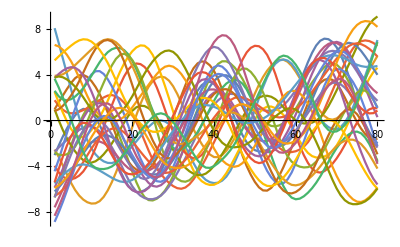

```mathematica
featYes =Table[reducedOxyYes80[[x,1]],{x,30}];
featNo =Table[reducedOxyNo80[[x,1]],{x,30}];
ListLinePlot[featYes ]
```

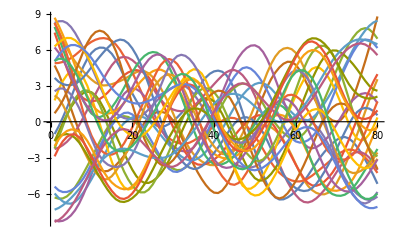

```mathematica
ListLinePlot[featNo]
```

### General Statistics

```mathematica
featExplore[f_]:=Histogram[{Table[f[reducedOxyNo80[[x,1]]],{x,30}],Table[f[reducedOxyYes80[[x,1]]],{x,30}]},ChartLabels->Placed[{"No","Yes"},Above],PlotLabel->f]
```

```mathematica
energy=Total@(#^2)&
stats={Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,energy}
```

Total[#1^2]&

{Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,Total[#1^2]&}

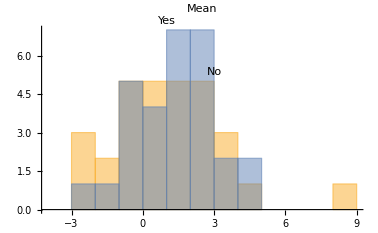
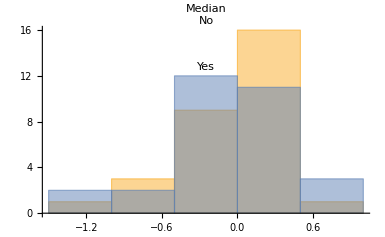
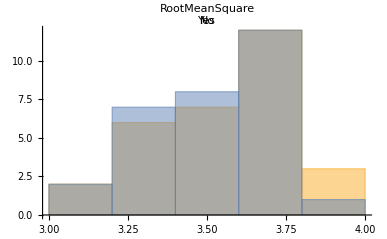
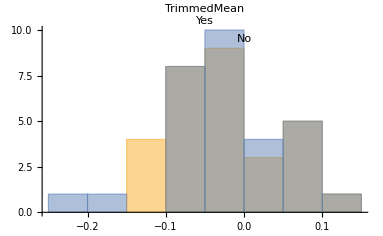
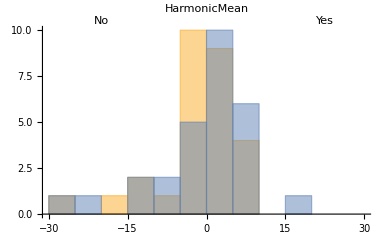
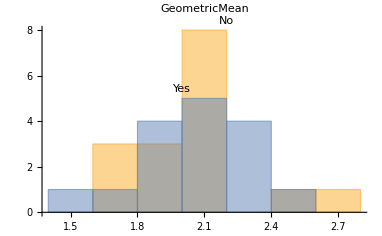
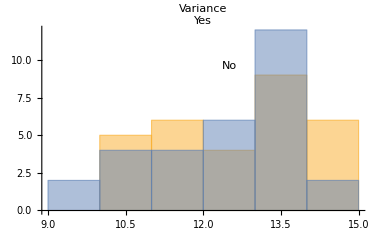
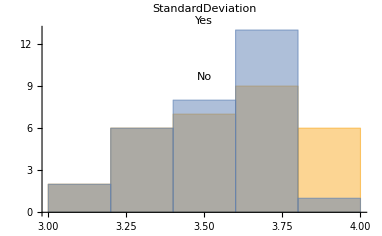
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column[Style[featExplore[#],Larger]&/@stats]
```

### Frequency Transforms

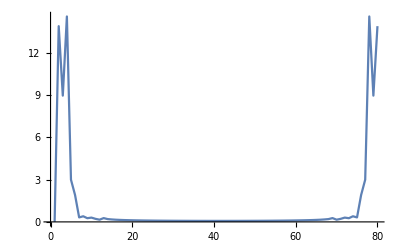

```mathematica
ListLinePlot[Abs[Fourier[reducedOxyYes80[[1,1]] ]],PlotRange->All]
```

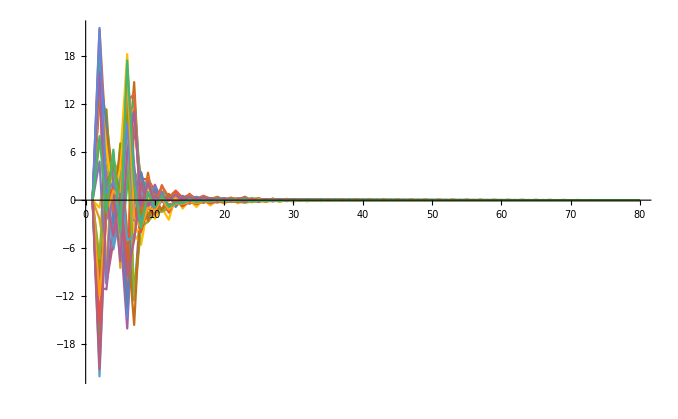

```mathematica
ListLinePlot[Table[FourierDCT[reducedOxyNo80[[x,1]] ],{x,30}],PlotRange->Full]
```

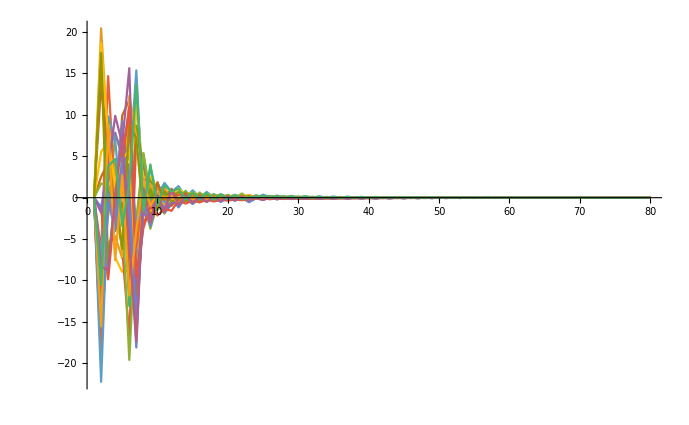

```mathematica
ListLinePlot[Table[FourierDCT[reducedOxyYes80[[x,1]] ],{x,30}],PlotRange->Full]
```

### Linear Interpolation Coefficient on First PCA element

```mathematica
getSlope[line_] := D[(line), var]
slopeNo = Table[getSlope[Fit[reducedOxyNo80[[x,1]], {1,var},var]],{x,30}];
slopeYes = Table[getSlope[Fit[reducedOxyYes80[[x,1]], {1,var},var]],{x,30}];
```

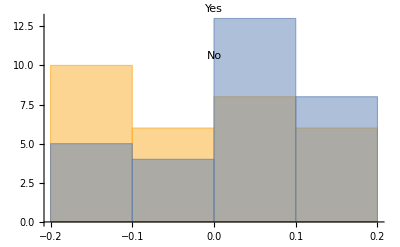

```mathematica
Histogram[{slopeNo,slopeYes},ChartLabels->Placed[{"No","Yes"},Above]]
```

### Quadratic Interpolation Coefficient on First PCA element

```mathematica
getSecondSlope[line_] := D[(D[(line), var]), var]
```

```mathematica
secondSlopeNo = Table[getSecondSlope[Fit[reducedOxyNo80[[x,1]], {1,var,var^2},var]],{x,30}];
secondSlopeYes = Table[getSecondSlope[Fit[reducedOxyYes80[[x,1]], {1,var,var^2},var]],{x,30}];
```

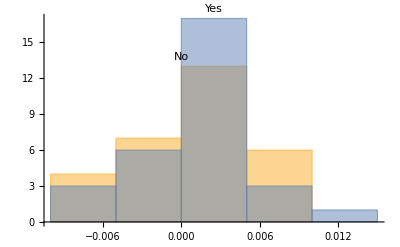

```mathematica
Histogram[{secondSlopeNo,secondSlopeYes},ChartLabels->Placed[{"No","Yes"},Above]]
```

### Linear Interpolation Coefficient on Second PCA element

```mathematica
slopeNoComp2 = Table[getSlope[Fit[reducedOxyNo80[[x,2]], {1,var},var]],{x,30}];
slopeYesComp2 = Table[getSlope[Fit[reducedOxyYes80[[x,2]], {1,var},var]],{x,30}];
```

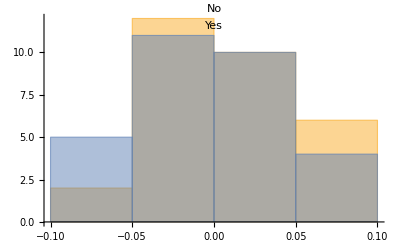

```mathematica
Histogram[{slopeNoComp2,slopeYesComp2},ChartLabels->Placed[{"No","Yes"},Above]]
```

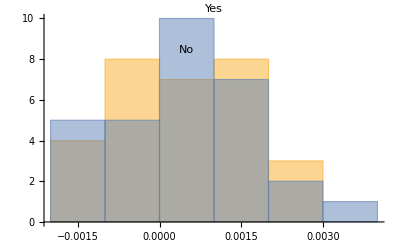

```mathematica
secondSlopeNoComp2 = Table[getSecondSlope[Fit[reducedOxyNo80[[x,2]], {1,var,var^2},var]],{x,30}];
secondSlopeYesComp2 = Table[getSecondSlope[Fit[reducedOxyYes80[[x,2]], {1,var,var^2},var]],{x,30}];
Histogram[{secondSlopeNoComp2,secondSlopeYesComp2},ChartLabels->Placed[{"No","Yes"},Above]]
```

## Selection of good examples as those that have positive drift

```mathematica
getLineSlope[line_] := D[(Fit[line, {1,var},var]), var]
```

```mathematica
getLineSlope[reducedOxyYes80[[1,1]]]
```

0.0790202

```mathematica
positiveDriftOxyYes = Select[reducedOxyYes80[[All,1]],getLineSlope[#]>0&];
Length[positiveDriftOxyYes]
```

21

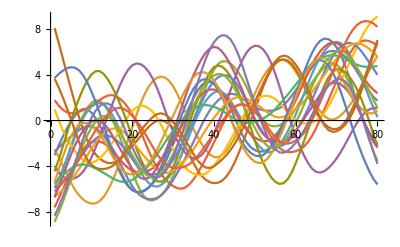

```mathematica
ListLinePlot[positiveDriftOxyYes]
```

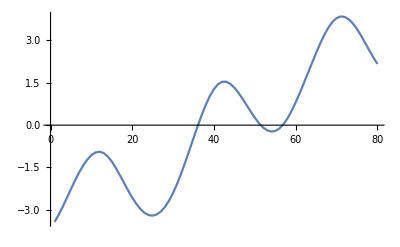

```mathematica
ListLinePlot[Mean[positiveDriftOxyYes]]
```

## Test with Cluster Classify

```mathematica
oxyYesCluster = ClusterClassify[reducedOxyYes80[[All,1]],1,Method->"KMeans"]
```

ClassifierFunction[…]

```mathematica
Options[oxyYesCluster]
```